```mathematica
Clear["Global`*"]
```

```mathematica
int1[y_,α_,x_,a_]:=(Integrate[q^2/(q^2+#1*y*q+α),q])/.q->x&@@{a}
```

```mathematica
int1[y,α,x,a]
```

x+((a^2 y^2-2 α) ArcTan[(2 x+a y)/(√(-a^2 y^2+4 α))])/(√(-a^2 y^2+4 α))-1/2 a y Log[x^2+a x y+α]

```mathematica
intq[R_,y_,α_,a_]:=(int1[y,α,R,#])-(int1[y,α,0,#])&@@{a}//Simplify
```

```mathematica
int2[R_,y_,α_,a_]:=Evaluate[Integrate[intq[R,y,α,q1],q1]]/.q1->a
```

```mathematica
intqθ[R_,y_,α_]:=(int2[#1,#2,#3,1])-(int2[#1,#2,#3,-1])&@@{R,y,α}//Simplify//Expand
ll[x1_,x2_,x3_]:=ll[x1,x2,x3]=Evaluate[2x1-Evaluate[intqθ[#1,#2,#3]&@@{x1,x2,x3}]//Simplify];
```

```mathematica
ll[x1,x2,x3];
```

```mathematica
L[R_,y_,α_]:=L[R,y,α]=ll[x1,x2,x3]/.{x1->R,x2->y,x3->α}
```

```mathematica
L[R,y,α]
```

(4 R y+2 y √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]+2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+2 R^2 Log[R^2-R y+α]-y^2 Log[R^2-R y+α]+2 α Log[R^2-R y+α]-2 R^2 Log[R^2+R y+α]+y^2 Log[R^2+R y+α]-2 α Log[R^2+R y+α])/(4 y)

```mathematica
f[Sqrt[α]]
```

f[√α]

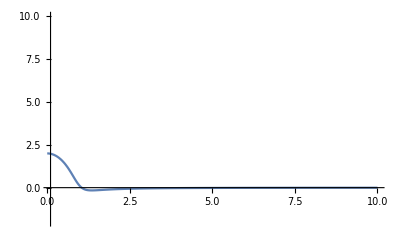

```mathematica
Plot[(f@@{x}/.{y->1.9,α->1}),{x,0,10},PlotRange->{{0.1,10},{-2,10}}]
```

```mathematica
int2
```

(2 a R y+2 a y √(-a^2 y^2+4 α) ArcTan[(a y)/(√(-a^2 y^2+4 α))]-2 a y √(-a^2 y^2+4 α) ArcTan[(2 R+a y)/(√(-a^2 y^2+4 α))]+a^2 y^2 Log[α]+2 R^2 Log[R^2+a R y+α]-a^2 y^2 Log[R^2+a R y+α]+2 α Log[R^2+a R y+α])/(4 y)

```mathematica
int1
```

x+((a^2 y^2-2 α) ArcTan[(2 x+a y)/(√(-a^2 y^2+4 α))])/(√(-a^2 y^2+4 α))-1/2 a y Log[x^2+a x y+α]

```mathematica
R^2-R y+α
```

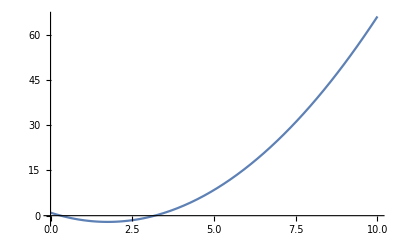

```mathematica
Plot[1-3.5 R+R^2,{R,0,10}]
```

```mathematica
Series[L[R,y],{y,0,1}]
```

2 √α ArcTan[R/(√α)]+O[y]^2

```mathematica
%//Simplify
```

((2 (y^2-3 α))/(3 R)+O[1/R]^3)+((1/(-y^2+4 α))^(1/2 Floor[Arg[((4 R-y) y)/(y^2-4 α)]/(2 π)]) (-y^2+4 α)^(1/2 Floor[Arg[((4 R-y) y)/(y^2-4 α)]/(2 π)])+(1/(-y^2+4 α))^(1/2 Floor[Arg[-(y (4 R+y))/(y^2-4 α)]/(2 π)]) (-y^2+4 α)^(1/2 Floor[Arg[-(y (4 R+y))/(y^2-4 α)]/(2 π)])) (-1/4 π (y^2-4 α) √(1/(-y^2+4 α))+O[1/R]^4)

```mathematica
L[R,y,α]
```

(4 R y+2 y √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]+2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+2 R^2 Log[R^2-R y+α]-y^2 Log[R^2-R y+α]+2 α Log[R^2-R y+α]-2 R^2 Log[R^2+R y+α]+y^2 Log[R^2+R y+α]-2 α Log[R^2+R y+α])/(4 y)

```mathematica
%//FullSimplify
```

R+1/2 √(-y^2+4 α) (-ArcTan[(-2 R+y)/(√(-y^2+4 α))]+ArcTan[(2 R+y)/(√(-y^2+4 α))])-((-2 R^2+y^2-2 α) (Log[R^2-R y+α]-Log[R (R+y)+α]))/(4 y)

```mathematica
Solve[(D[-ArcTan[(-2 R+y)/(√(-y^2+4 α))]+ArcTan[(2 R+y)/(√(-y^2+4 α))],R]//FullSimplify)==0,R]
```

{{R→-ⅈ √α},{R→ⅈ √α}}

```mathematica
D[-ArcTan[(-2 R+y)/(√(-y^2+4 α))]+ArcTan[(2 R+y)/(√(-y^2+4 α))],R]//FullSimplify
```

((R^2+α) √(-y^2+4 α))/((R^2-R y+α) (R (R+y)+α))

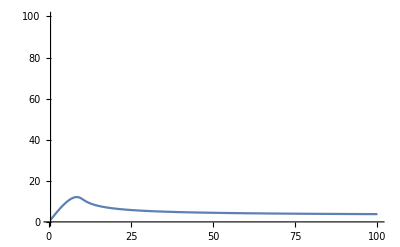

```mathematica
Plot[L[R,y,α]/.{R->x,y->19.9,α->100},{x,0.5,100},PlotRange->{{0.5,100},{0,100}}]
```

```mathematica
L[0,y,α]
```

0

```mathematica
Evaluate[L[R,1.9,1]]
```

$Aborted[]

```mathematica
L@@{R,1,1}
```

1/4 (4 R+2 √3 ArcTan[(-1+2 R)/(√3)]+2 √3 ArcTan[(1+2 R)/(√3)]+Log[1-R+R^2]+2 R^2 Log[1-R+R^2]-Log[1+R+R^2]-2 R^2 Log[1+R+R^2])

```mathematica
L[R,y,α]//FullSimplify
```

(R+1/2 √(-y^2+4 α) (-ArcTan[(-2 R+y)/(√(-y^2+4 α))]+ArcTan[(2 R+y)/(√(-y^2+4 α))])-((-2 R^2+y^2-2 α) (Log[R^2-R y+α]-Log[R (R+y)+α]))/(4 y))[R,y,α][R,y,α]

```mathematica
L
```

(4 R y+2 y √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]+2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+2 R^2 Log[R^2-R y+α]-y^2 Log[R^2-R y+α]+2 α Log[R^2-R y+α]-2 R^2 Log[R^2+R y+α]+y^2 Log[R^2+R y+α]-2 α Log[R^2+R y+α])/(4 y)

```mathematica
D[(R^2+R y+α)/(R^2-R y+α),R]//Simplify
```

(2 y (-R^2+α))/((R^2-R y+α)^2)

```mathematica
Solve[%==0,R]
```

{{R→-√α},{R→√α}}

```mathematica
D[(R^2+α-y^2/2)/(R^2-R y+α),R]//Simplify
```

-(y (2 R^2-2 R y+y^2-2 α))/(2 (R^2-R y+α)^2)

```mathematica
Solve[%==0,R]
```

{{R→1/2 (y-√(-y^2+4 α))},{R→1/2 (y+√(-y^2+4 α))}}

```mathematica
(R^2+α-y^2/2)((2R)/(R^2-R y+α)-(2(R)^2y)/((R^2-R y+α)^2)+(2^3/3(R)^3y^2)/((R^2-R y+α)^3))//FullSimplify
```

(R (2 R^2-y^2+2 α) (3 R^4-9 R^3 y-9 R y α+3 α^2+2 R^2 (5 y^2+3 α)))/(3 (R^2-R y+α)^3)

```mathematica
%//Expand
```

(2 R^7)/((R^2-R y+α)^3)-(6 R^6 y)/((R^2-R y+α)^3)+(17 R^5 y^2)/(3 (R^2-R y+α)^3)+(3 R^4 y^3)/((R^2-R y+α)^3)-(10 R^3 y^4)/(3 (R^2-R y+α)^3)+(6 R^5 α)/((R^2-R y+α)^3)-(12 R^4 y α)/((R^2-R y+α)^3)+(14 R^3 y^2 α)/(3 (R^2-R y+α)^3)+(3 R^2 y^3 α)/((R^2-R y+α)^3)+(6 R^3 α^2)/((R^2-R y+α)^3)-(6 R^2 y α^2)/((R^2-R y+α)^3)-(R y^2 α^2)/((R^2-R y+α)^3)+(2 R α^3)/((R^2-R y+α)^3)

```mathematica
%//Simplify
```

(R (6 R^6-18 R^5 y+9 R y (y^2-2 α) α-3 (y^2-2 α) α^2+R^4 (17 y^2+18 α)+9 R^3 (y^3-4 y α)-2 R^2 (5 y^4-7 y^2 α-9 α^2)))/(3 (R^2-R y+α)^3)

```mathematica
%//FullSimplify
```

2 (y (2+(6 α)/(y^2-4 α))+(y^4-8 y^2 α+8 α^2)/((-y^2+4 α)^(3/2)))

```mathematica
%//Simplify
```

(y^2-4 α-y √(-y^2+4 α))/(y^2-4 α)

```mathematica
Series[Log[1+x],{x,0,4}]
```

x-x^2/2+x^3/3-x^4/4+O[x]^5

```mathematica
D[(R (2 R^2-y^2+2 α) (3 R^4-9 R^3 y-9 R y α+3 α^2+2 R^2 (5 y^2+3 α)))/(3 (R^2-R y+α)^3),R]
```

(R (2 R^2-y^2+2 α) (12 R^3-27 R^2 y-9 y α+4 R (5 y^2+3 α)))/(3 (R^2-R y+α)^3)+(4 R^2 (3 R^4-9 R^3 y-9 R y α+3 α^2+2 R^2 (5 y^2+3 α)))/(3 (R^2-R y+α)^3)-(R (2 R-y) (2 R^2-y^2+2 α) (3 R^4-9 R^3 y-9 R y α+3 α^2+2 R^2 (5 y^2+3 α)))/((R^2-R y+α)^4)+((2 R^2-y^2+2 α) (3 R^4-9 R^3 y-9 R y α+3 α^2+2 R^2 (5 y^2+3 α)))/(3 (R^2-R y+α)^3)

```mathematica
%//Simplify
```

(6 R^8-24 R^7 y-72 R^3 y α^2+12 R y (y^2-2 α) α^2-3 (y^2-2 α) α^3+R^6 (37 y^2+24 α)-4 R^5 (13 y^3+18 y α)+3 R^2 α (-7 y^4+13 y^2 α+8 α^2)+R^4 (21 y^4+79 y^2 α+36 α^2))/(3 (R^2-R y+α)^4)

```mathematica
D[((R^2-2 R y+α) (2 R^2-y^2+2 α))/((R^2-R y+α)^2),R]
```

(4 R (R^2-2 R y+α))/((R^2-R y+α)^2)-(2 (2 R-y) (R^2-2 R y+α) (2 R^2-y^2+2 α))/((R^2-R y+α)^3)+((2 R-2 y) (2 R^2-y^2+2 α))/((R^2-R y+α)^2)

```mathematica
Solve[%==0,R]
```

{{R→0},{R→1/6 (3 y-√3 √(-y^2+4 α))},{R→1/6 (3 y+√3 √(-y^2+4 α))}}

```mathematica
((R^2-2 R y+α) (2 R^2-y^2+2 α))/((R^2-R y+α)^2)/.{R->1/6 (3 y-√3 √(-y^2+4 α))}//FullSimplify
```

```mathematica
(13 y^4-68 y^2 α+64 α^2+3 √3 y^3 √(-y^2+4 α))/(2 (y^2-4 α)^2)/.α->1
```

(64-68 y^2+13 y^4+3 √3 y^3 √(4-y^2))/(2 (-4+y^2)^2)

```mathematica
Solve[%218==2,y]
```

{{y→0},{y→√3}}

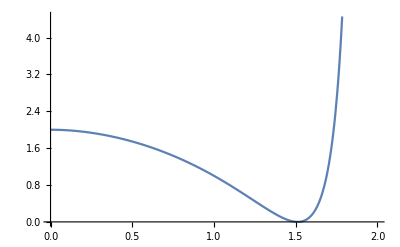

```mathematica
Plot[%,{y,0,2}]
```

```mathematica
((R^2-2 R y+α) (2 R^2-y^2+2 α))/((R^2-R y+α)^2)/.{R->0}//FullSimplify
```

2-y^2/α

```mathematica
3 √3 y^3 √(-y^2+4 y^2/2)//Simplify
```

3 √3 y^3 √(y^2)

```mathematica
%//FullSimplify
```

3 √3 y^3 √(y^2)

```mathematica
3Sqrt[3]//N
```

5.19615

```mathematica
Manipulate[Manipulate[Manipulate[L[R,y,α]//N,{R,0,100}],{α,4y^2,1000}],{y,0,10}]
```

```mathematica
L[3,10,α]
```

1/20 (60-20 √(-25+α) ArcTan[2/(√(-25+α))]+20 √(-25+α) ArcTan[8/(√(-25+α))]-41 Log[-21+α]+α Log[-21+α]+41 Log[39+α]-α Log[39+α])

```mathematica
Evaluate[L[100,10,α]]
```

100+√(-25+α) ArcTan[95/(√(-25+α))]+√(-25+α) ArcTan[105/(√(-25+α))]+1/20 (9950+α) Log[9000+α]-995/2 Log[11000+α]-1/20 α Log[11000+α]

```mathematica
L[100,10,α]
```

100+√(-25+α) ArcTan[95/(√(-25+α))]+√(-25+α) ArcTan[105/(√(-25+α))]+1/20 (9950+α) Log[9000+α]-995/2 Log[11000+α]-1/20 α Log[11000+α]

```mathematica
L[R,y,α]
```

(4 R y+2 y √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]+2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+2 R^2 Log[R^2-R y+α]-y^2 Log[R^2-R y+α]+2 α Log[R^2-R y+α]-2 R^2 Log[R^2+R y+α]+y^2 Log[R^2+R y+α]-2 α Log[R^2+R y+α])/(4 y)

```mathematica
%/.{R->100,y->10}
```

1/40 (4000+20 √(-100+4 α) ArcTan[190/(√(-100+4 α))]+20 √(-100+4 α) ArcTan[210/(√(-100+4 α))]+19900 Log[9000+α]+2 α Log[9000+α]-19900 Log[11000+α]-2 α Log[11000+α])

```mathematica
Evaluate[L[100,10,26]]
```

ArcTan[95]+ArcTan[105]+1/10 (25 (40+Log[5513/4513])+5013 Log[4513]-5013 Log[5513])

```mathematica
Clear[f]
```

```mathematica
L[R,y,α]
```

1/(4 y)(4 R y+2 y √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]+2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+8 y Integrate[0,0,Assumptions→True]+2 R^2 Log[R^2-R y+α]-y^2 Log[R^2-R y+α]+2 α Log[R^2-R y+α]-2 R^2 Log[R^2+R y+α]+y^2 Log[R^2+R y+α]-2 α Log[R^2+R y+α])

```mathematica
f[R_,y_,α_]:=L[#1,#2,#3]&@@{R,y,α}
```

```mathematica
f[26]
```

f[26]

```mathematica
f[x]
```

```mathematica
Manipulate[Manipulate[Plot[{L[R,y,x],Pi*Sqrt[x]},{x,y^2/4,10000000}],{R,0,1000000}],{y,1,1000}]
```

```mathematica
Manipulate[Manipulate[Plot[{L[R,1.9,1]},{R,0,100},PlotRange->{{0,100},{0,10}}],{x,y^2/4,10000000}],{y,1,1000}]
```

```mathematica
D[L[R,y,α],R]//FullSimplify
```

(2 y+R Log[R^2-R y+α]-R Log[R (R+y)+α])/y

```mathematica
Solve[2 y+R Log[R^2-R y+α]-R Log[R (R+y)+α]==0,R]
```

Solve[2 y+R Log[R^2-R y+α]-R Log[R (R+y)+α]==0,R]

```mathematica
L[R,y,α]//FullSimplify
```

R+1/2 √(-y^2+4 α) (-ArcTan[(-2 R+y)/(√(-y^2+4 α))]+ArcTan[(2 R+y)/(√(-y^2+4 α))])-((-2 R^2+y^2-2 α) (Log[R^2-R y+α]-Log[R (R+y)+α]))/(4 y)

```mathematica
2+(R Log[R^2-R y+α]-R Log[R (R+y)+α])/y//TeXForm
```

\frac{R \log \left(\alpha +R^2-R y\right)-R \log (\alpha +R (R+y))}{y}+2

```mathematica
(Pi(-Sqrt[α])/(y*Sqrt[4α-y^2]))/(1+2Sqrt[1+((-Sqrt[α])/(y*Sqrt[4α-y^2]))^2])+(3(2α+y^2)/(y*Sqrt[4α-y^2]))/(1+2Sqrt[1+((2α+y^2)/(y*Sqrt[4α+y^2]))^2])
```

-(π √α)/(y √(-y^2+4 α) (1+2 √(1+α/(y^2 (-y^2+4 α)))))+(3 (y^2+2 α))/(y √(-y^2+4 α) (1+2 √(1+((y^2+2 α)^2)/(y^2 (y^2+4 α)))))

```mathematica
%//Simplify
```

((3 (y^2+2 α))/(1+2 √2 √((y^4+4 y^2 α+2 α^2)/(y^4+4 y^2 α)))-(π √α)/(1+2 √(1-α/(y^4-4 y^2 α))))/(y √(-y^2+4 α))

```mathematica
%^2
```

(((3 (y^2+2 α))/(1+2 √2 √((y^4+4 y^2 α+2 α^2)/(y^4+4 y^2 α)))-(π √α)/(1+2 √(1-α/(y^4-4 y^2 α))))^2)/(y^2 (-y^2+4 α))

```mathematica
%//Simplify
```

((-(3 (y^2+2 α))/(1+2 √2 √((y^4+4 y^2 α+2 α^2)/(y^4+4 y^2 α)))+(π √α)/(1+2 √(1-α/(y^4-4 y^2 α))))^2)/(y^2 (-y^2+4 α))

```mathematica
%//FullSimplify
```

((-(3 (y^2+2 α))/(1+2 √(7/4+α/y^2+y^2/(4 (y^2+4 α))))+(π √α)/(1+2 √(1-α/(y^4-4 y^2 α))))^2)/(y^2 (-y^2+4 α))

```mathematica
Sqrt[4α-y^2]%//Simplify
```

(y^6+18 y^4 α-36 y^2 α^2+8 α^3)/(3 y^5-12 y^3 α)

```mathematica
%//FullSimplify
```

(y^6+18 y^4 α-36 y^2 α^2+8 α^3)/(3 y^5-12 y^3 α)

```mathematica
(Sqrt[α]-y)/Sqrt[4α-y^2]+(Sqrt[α]+y)/Sqrt[4α-y^2]-1/3((Sqrt[α]+y)/Sqrt[4α-y^2])^3
```

-(y+√α)^3/(3 (-y^2+4 α)^(3/2))+(-y+√α)/(√(-y^2+4 α))+(y+√α)/(√(-y^2+4 α))

```mathematica
%//Simplify
```

-(y^3+9 y^2 √α+3 y α-23 α^(3/2))/(3 (-y^2+4 α)^(3/2))

```mathematica
%//FullSimplify
```

-(y^3+9 y^2 √α+3 y α-23 α^(3/2))/(3 (-y^2+4 α)^(3/2))

```mathematica
g[x_,y_,z_]:=x-(2x^2-y^2+2z)/(4y)Log[(x^2+x*y+z)/(x^2-x*y+z)];
```

```mathematica
h[x_,y_,z_]:=(2 x^4+(y^2-2 z) z+x^2 (-3 y^2+8 z));
```

```mathematica
2/3 Sqrt[5]-0.2
```

1.29071

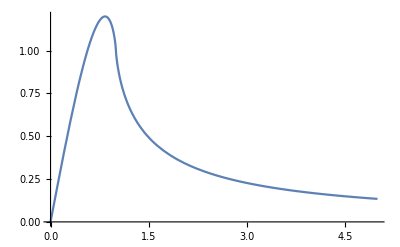

```mathematica
Plot[g[x,2,1],{x,0,5}]
```

```mathematica
g[R,y,α]//FullSimplify
```

```mathematica
R+((-2 R^2+y^2-2 α)(2 R y (R^2+α) (2 R^2-y^2+2 α))/((R^2-R y+α) (R (R+y)+α))1/(2 R^2+y^2+2 α))/(4 y)
```

R+(R (-2 R^2+y^2-2 α) (R^2+α) (2 R^2-y^2+2 α))/(2 (R^2-R y+α) (R (R+y)+α) (2 R^2+y^2+2 α))

```mathematica
%//FullSimplify
```

R-(R (-2 R^2+y^2-2 α)^2 (R^2+α))/(2 (R^2-R y+α) (R (R+y)+α) (2 R^2+y^2+2 α))

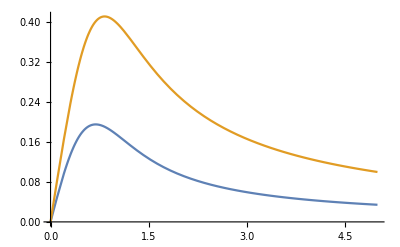

```mathematica
Plot[{g[R,1,1],Evaluate[%89/.{y->1,α->1}]},{R,0,5}]
```

```mathematica
g[1,1000000,1000000^2]//N
```

0.5

```mathematica
g[R,y,α]
```

```mathematica
R-((2 R^2-y^2+2 α)(2 R y (R^2+α) (2 R^2-y^2+2 α))/((R^2-R y+α) (R (R+y)+α))1/(2 R^2+y^2+2 α))/(4 y)
```

R-(R (R^2+α) (2 R^2-y^2+2 α)^2)/(2 (R^2-R y+α) (R (R+y)+α) (2 R^2+y^2+2 α))

```mathematica
%//FullSimplify
```

R-(R (-2 R^2+y^2-2 α)^2 (R^2+α))/(2 (R^2-R y+α) (R (R+y)+α) (2 R^2+y^2+2 α))

```mathematica
%/.{y->yy}
```

R-(R (-2 R^2+yy^2-2 α)^2 (R^2+α))/(2 (R^2-R yy+α) (R (R+yy)+α) (2 R^2+yy^2+2 α))

```mathematica
%//TeXForm
```

R-\frac{R \left(\alpha +R^2\right) \left(-2 \alpha -2 R^2+\text{yy}^2\right)^2}{2 \left(\alpha +R^2-R \text{yy}\right) (\alpha +R (R+\text{yy})) \left(2 \alpha +2 R^2+\text{yy}^2\right)}

```mathematica
D[g[R,y,α],y]//FullSimplify
```

(-(2 R y (R^2+α) (2 R^2-y^2+2 α))/((R^2-R y+α) (R (R+y)+α))+(2 R^2+y^2+2 α) Log[1+(2 R y)/(R^2-R y+α)])/(4 y^2)

```mathematica
%/.{y->yy}
```

(-(2 R yy (R^2+α) (2 R^2-yy^2+2 α))/((R^2-R yy+α) (R (R+yy)+α))+(2 R^2+yy^2+2 α) Log[1+(2 R yy)/(R^2-R yy+α)])/(4 yy^2)

```mathematica
%//TeXForm
```

\frac{\left(2 \alpha +2 R^2+\text{yy}^2\right) \log \left(\frac{2 R \text{yy}}{\alpha +R^2-R \text{yy}}+1\right)-\frac{2 R \text{yy} \left(\alpha +R^2\right) \left(2 \alpha +2
   R^2-\text{yy}^2\right)}{\left(\alpha +R^2-R \text{yy}\right) (\alpha +R (R+\text{yy}))}}{4 \text{yy}^2}

```mathematica
D[(-2 R^2+y^2-2 α) Log[1+(2 R y)/(R^2-R y+α)],y]
```

((-2 R^2+y^2-2 α) ((2 R^2 y)/((R^2-R y+α)^2)+(2 R)/(R^2-R y+α)))/(1+(2 R y)/(R^2-R y+α))+2 y Log[1+(2 R y)/(R^2-R y+α)]

```mathematica
(-2 R^2+y^2-2 α)(((-2 R^2+y^2-2 α) ((2 R^2 y)/((R^2-R y+α)^2)+(2 R)/(R^2-R y+α)))/(1+(2 R y)/(R^2-R y+α)))/(2y)
```

((-2 R^2+y^2-2 α)^2 ((2 R^2 y)/((R^2-R y+α)^2)+(2 R)/(R^2-R y+α)))/(2 y (1+(2 R y)/(R^2-R y+α)))

```mathematica
%//FullSimplify
```

(R (-2 R^2+y^2-2 α)^2 (R^2+α))/(y (R^2-R y+α) (R (R+y)+α))

```mathematica
Solve[%==0,y]
```

{{y→-√2 √(R^2+α)},{y→-√2 √(R^2+α)},{y→√2 √(R^2+α)},{y→√2 √(R^2+α)}}

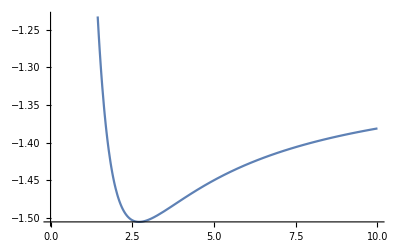

```mathematica
Plot[Evaluate[%/.{y->1.3,α->1}],{R,0,10}]
```

```mathematica
%//FullSimplify
```

R+(π R (-2 R^2+y^2-2 α))/(2 (R^2-R y+α) (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2))))

```mathematica
D[%,R]
```

1-(π R (-2 R^2+y^2-2 α) (-(8 R^2 (2 R-y) y^2)/((R^2-R y+α)^3)+(8 R y^2)/((R^2-R y+α)^2)))/(2 (R^2-R y+α) √(1+(4 R^2 y^2)/((R^2-R y+α)^2)) (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))^2)-(π R (2 R-y) (-2 R^2+y^2-2 α))/(2 (R^2-R y+α)^2 (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2))))-(2 π R^2)/((R^2-R y+α) (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2))))+(π (-2 R^2+y^2-2 α))/(2 (R^2-R y+α) (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2))))

```mathematica
%//FullSimplify
```

1/2 (2-(8 π R^2 y^2 (R^2-α) (2 R^2-y^2+2 α))/((R^2-R y+α)^4 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)) (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))^2)-(4 π R^2)/((R^2-R y+α) (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2))))+(π (-2 R^2+y^2-2 α))/((R^2-R y+α) (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2))))+(π R (2 R-y) (2 R^2-y^2+2 α))/((R^2-R y+α)^2 (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))))

```mathematica
%^2
```

(R+(π R (-2 R^2+y^2-2 α))/(2 (R^2-R y+α) (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))))^2

```mathematica
%//Expand//Simplify
```

(R^2 (2 R^2-2 π R^2-2 R y+π y^2+2 α-2 π α+4 R^2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2))-4 R y √(1+(4 R^2 y^2)/((R^2-R y+α)^2))+4 α √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))^2)/(4 (R^2-R y+α)^2 (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))^2)

```mathematica
%//FullSimplify
```

(R^2 (π y^2+2 α-2 π α+4 α √(1+(4 R^2 y^2)/((R^2-R y+α)^2))+R^2 (2-2 π+4 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))-2 R (y+2 y √(1+(4 R^2 y^2)/((R^2-R y+α)^2))))^2)/(4 (R^2-R y+α)^2 (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))^2)

```mathematica
D[%35,R]//Simplify
```

1/(2 (R^2-R y+α)^3 (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))^3)R (π y^2+2 α-2 π α+4 α √(1+(4 R^2 y^2)/((R^2-R y+α)^2))+R^2 (2-2 π+4 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))-2 R (y+2 y √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))) ((8 R^2 y^2 (R^2-α) (2 R^2-2 π R^2-2 R y+π y^2+2 α-2 π α+4 R^2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2))-4 R y √(1+(4 R^2 y^2)/((R^2-R y+α)^2))+4 α √(1+(4 R^2 y^2)/((R^2-R y+α)^2))))/((R^2-R y+α)^2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))-R (2 R-y) (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2))) (π y^2+2 α-2 π α+4 α √(1+(4 R^2 y^2)/((R^2-R y+α)^2))+R^2 (2-2 π+4 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))-2 R (y+2 y √(1+(4 R^2 y^2)/((R^2-R y+α)^2))))+(R^2-R y+α) (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2))) (π y^2+2 α-2 π α+4 α √(1+(4 R^2 y^2)/((R^2-R y+α)^2))+R^2 (2-2 π+4 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))-2 R (y+2 y √(1+(4 R^2 y^2)/((R^2-R y+α)^2))))-(2 R (1+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2))) (8 R^2 y^2 (R^3-R α)-8 R y^3 (R^3-R α)-8 y^2 α (-R^3+R α)-2 R (R^2-R y+α)^3 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)) (1-π+2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))+(R^2-R y+α)^3 √(1+(4 R^2 y^2)/((R^2-R y+α)^2)) (y+2 y √(1+(4 R^2 y^2)/((R^2-R y+α)^2)))))/((R^2-R y+α)^2 √(1+(4 R^2 y^2)/((R^2-R y+α)^2))))

```mathematica
%42//FullSimplify
```

$Aborted

```mathematica
Solve[%==0,R]
```

$Aborted

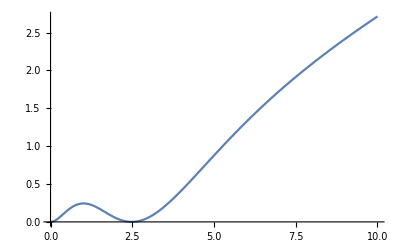

```mathematica
Plot[Evaluate[%35/.{y->1.4,α->1}],{R,0,10}]
```

```mathematica
R+((-2 R^2+y^2-2 α) y/R(4 R^4+y^2 α+R^2 (-3 y^2+4 α))/(2 (R^2-R y+α) (R (R+y)+α)))/(4 y)//FullSimplify
```

(y^2 (2 R^4+(y^2-2 α) α+R^2 (-3 y^2+8 α)))/(8 R (R^2-R y+α) (R (R+y)+α))

```mathematica
%/.R->y/2
```

(y (y^4/8+(y^2-2 α) α+1/4 y^2 (-3 y^2+8 α)))/(4 (-y^2/4+α) ((3 y^2)/4+α))

```mathematica
%//Simplify
```

(5 y^3-4 y α)/(6 y^2+8 α)

```mathematica
R+((-2 R^2+y^2-2 α) (2 R y)/(R^2-R y+α))/(4 y)//FullSimplify
```

(R y (-2 R+y))/(2 (R^2-R y+α))

```mathematica
%//FullSimplify
```

```mathematica
(4 R^4+y^2 α+R^2 (-3 y^2+4 α))/(2 (R^2-R y+α) (R (R+y)+α))-(R (2 R y)/(R^2-R y+α))/y
```

-(2 R^2)/(R^2-R y+α)+(4 R^4+y^2 α+R^2 (-3 y^2+4 α))/(2 (R^2-R y+α) (R (R+y)+α))

```mathematica
%//FullSimplify
```

(y (-4 R^3-3 R^2 y+y α))/(2 (R^2-R y+α) (R (R+y)+α))

```mathematica
-((R^2-R y+α) (2 R^2-y^2+2 α) (R/(R^2-R y+α)+(R (R^2+R y+α))/((R^2-R y+α)^2)))/(4 y (R^2+R y+α))+1/2 y/R(4 R^4+y^2 α+R^2 (-3 y^2+4 α))/(2 (R^2-R y+α) (R (R+y)+α))+((2 R^2-y^2+2 α) y/R(4 R^4+y^2 α+R^2 (-3 y^2+4 α))/(2 (R^2-R y+α) (R (R+y)+α)))/(4 y^2)//FullSimplify
```

(y (2 R^4+α (y^2+2 α)+R^2 (-3 y^2+4 α)))/(8 R (R^2-R y+α) (R (R+y)+α))

```mathematica
D[g[R,y,α],R]//FullSimplify
```

(4 R^4+y^2 α+R^2 (-3 y^2+4 α))/(2 (R^2-R y+α) (R (R+y)+α))-(R Log[1+(2 R y)/(R^2-R y+α)])/y

```mathematica
D[g[R,y,α],R]
R+((-2 R^2) ((2 R y)/(R^2-R y+α))/(1+(2 R y)/(R^2-R y+α)))/(4 y)//FullSimplify
```

1-((R^2-R y+α) (2 R^2-y^2+2 α) ((2 R+y)/(R^2-R y+α)-((2 R-y) (R^2+R y+α))/((R^2-R y+α)^2)))/(4 y (R^2+R y+α))-(R Log[(R^2+R y+α)/(R^2-R y+α)])/y

(R (R y+α))/(R (R+y)+α)

```mathematica
((2 R y)/(R^2-R y+α))/(1+(2 R y)/(R^2-R y+α))//FullSimplify
```

(2 R y)/(R (R+y)+α)

```mathematica
h1[R_,y_,α_]:=(R y (-2 R+y))/(2 (R^2-R y+α));
```

```mathematica
h2[R_,y_,α_]:=(R y (2 R+y))/(2 (R (R+y)+α));
h3[R_,y_,α_]:=R-((2 R^2-y^2+2 α) y/R(4 R^4+y^2 α+R^2 (-3 y^2+4 α))/(2 (R^2-R y+α) (R (R+y)+α)))/(4 y)
```

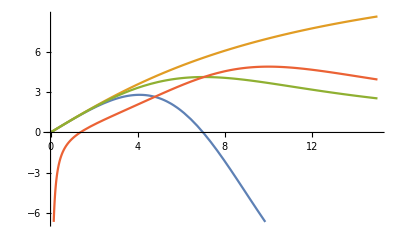

```mathematica
Plot[{h1[R,14,100],h2[R,14,100],g[R,14,100],h3[R,14,100]},{R,0,15}]
```

```mathematica
h3[R,y,α]//FullSimplify
```

(y^2 (2 R^4+(y^2-2 α) α+R^2 (-3 y^2+8 α)))/(8 R (R^2-R y+α) (R (R+y)+α))

```mathematica
(2 R^4+(y^2-2 α) α+R^2 (-3 y^2+8 α))/.{R->1/2 √(3 y^2-8 α)}
```

1/8 (3 y^2-8 α)^2+(y^2-2 α) α+1/4 (3 y^2-8 α) (-3 y^2+8 α)

```mathematica
%//Simplify
```

```mathematica
-(9 y^4)/8+7 y^2 α-10 α^2//TeXForm
```

-10 \alpha ^2-\frac{9 y^4}{8}+7 \alpha  y^2

```mathematica
%/.{y->Sqrt[2α]}
```

-α^2/2

```mathematica
7^2-4*10*9/8
```

4

```mathematica
45/16//N
```

2.8125

```mathematica
5*8/18//N
```

2.22222

```mathematica
(8/3)//N
```

2.66667

```mathematica
%//N
```

7.11111

```mathematica
Solve[-(9 y^4)/8+7 y^2 α-10 α^2==0,y]
```

{{y→-2 √α},{y→2 √α},{y→-2/3 √5 √α},{y→(2 √5 √α)/3}}

```mathematica
2 R^4+(y^2-2 α) α+R^2 (-3 y^2+8 α)
D[2 R^4+(y^2-2 α) α+R^2 (-3 y^2+8 α),R]
```

2 R^4+(y^2-2 α) α+R^2 (-3 y^2+8 α)

8 R^3+2 R (-3 y^2+8 α)

```mathematica
Solve[%==0,R]
```

{{R→0},{R→-1/2 √(3 y^2-8 α)},{R→1/2 √(3 y^2-8 α)}}

```mathematica
g[100000,1,1]
```

100000-20000000001/4 Log[10000100001/9999900001]

```mathematica
D[D[g[R,y,α],R],R]//FullSimplify
```

```mathematica
(2 R^7-3 R^5 (y^2-2 α)+6 R^3 α^2+R α (y^4-5 y^2 α+2 α^2))/((R^2-R y+α)^2 (R (R+y)+α)^2)-((4 R^4+y^2 α+R^2 (-3 y^2+4 α))/(2 (R^2-R y+α) (R (R+y)+α)))/R
```

-(4 R^4+y^2 α+R^2 (-3 y^2+4 α))/(2 R (R^2-R y+α) (R (R+y)+α))+(2 R^7-3 R^5 (y^2-2 α)+6 R^3 α^2+R α (y^4-5 y^2 α+2 α^2))/((R^2-R y+α)^2 (R (R+y)+α)^2)

```mathematica
%//FullSimplify
```

(y^2 (R^2-α) (R^4+α^2+R^2 (-3 y^2+10 α)))/(2 R (R^2-R y+α)^2 (R (R+y)+α)^2)

```mathematica
Solve[x^2+α^2+x (-3 y^2+10 α)==0,x]
```

{{x→1/2 (3 y^2-10 α-√3 √(3 y^4-20 y^2 α+32 α^2))},{x→1/2 (3 y^2-10 α+√3 √(3 y^4-20 y^2 α+32 α^2))}}

```mathematica
D[g[R,y,α],R]
```

1-((R^2-R y+α) (2 R^2-y^2+2 α) ((2 R+y)/(R^2-R y+α)-((2 R-y) (R^2+R y+α))/((R^2-R y+α)^2)))/(4 y (R^2+R y+α))-(R Log[(R^2+R y+α)/(R^2-R y+α)])/y

```mathematica
g[R,y,α]
```

R-((2 R^2-y^2+2 α) Log[(R^2+R y+α)/(R^2-R y+α)])/(4 y)

```mathematica
Solve[R-((2 R^2-y^2+2 α) (2 R y)/(R^2-R y+α))/(4 y)==0,R]
```

{{R→0},{R→y/2}}

```mathematica
%//Simplify
```

(R y (-2 R+y))/(2 (R^2-R y+α))

```mathematica
%//Simplify
```

(y (-4 R^3-3 R^2 y+y α))/(2 (R^2-R y+α) (R^2+R y+α))

```mathematica
%//TeXForm
```

\frac{4 R^4+R^2 \left(4 \alpha -3 y^2\right)+\alpha  y^2}{2 \left(\alpha +R^2-R y\right) (\alpha +R (R+y))}-\frac{R \log \left(\frac{2 R y}{\alpha +R^2-R y}+1\right)}{y}

```mathematica
Solve[%==0,x]
```

```mathematica
g[x,y,z]//FullSimplify
```

```mathematica
x+((-2 x^2+y^2-2 z) (2 x y)/(x^2-x y+z))/(4 y)//FullSimplify
```

(x y (-2 x+y))/(2 (x^2-x y+z))

```mathematica
x+((-2 x^2+y^2-2 z) 1/(2 x^2+y^2+2 z)(2 x y (x^2+z) (2 x^2-y^2+2 z))/((x^2-x y+z) (x (x+y)+z)))/(4 y)//FullSimplify
```

x-(x (-2 x^2+y^2-2 z)^2 (x^2+z))/(2 (x^2-x y+z) (x (x+y)+z) (2 x^2+y^2+2 z))

```mathematica
Solve[%==0,y]
```

{{y→0},{y→0},{y→-(√2 √(x^4+4 x^2 z+3 z^2))/(√(3 x^2+z))},{y→(√2 √(x^4+4 x^2 z+3 z^2))/(√(3 x^2+z))}}

```mathematica
x+((-2 x^2+y^2-2 z) y/x(4 x^4+y^2 z+x^2 (-3 y^2+4 z))/(2 (x^2-x y+z) (x (x+y)+z)))/(4 y)//Simplify
```

(y^2 (2 x^4+(y^2-2 z) z+x^2 (-3 y^2+8 z)))/(8 x (x^2-x y+z) (x^2+x y+z))

```mathematica
%/.{x->R,y->Abs[y],x->α}
```

(Abs[y]^2 (2 R^4+R^2 (8 z-3 Abs[y]^2)+z (-2 z+Abs[y]^2)))/(8 R (R^2+z-R Abs[y]) (R^2+z+R Abs[y]))

```mathematica
%//TeXForm
```

\frac{\left| y\right| ^2 \left(R^2 \left(8 z-3 \left| y\right| ^2\right)+z \left(\left| y\right| ^2-2 z\right)+2 R^4\right)}{8 R \left(-R \left| y\right| +R^2+z\right) \left(R \left| y\right| +R^2+z\right)}

```mathematica
x+((-2 x^2+y^2-2 z) (4 x^4+y^2 z+x^2 (-3 y^2+4 z)))/(8 x (x^2-x y+z) (x (x+y)+z))//Expand
```

x-x^5/((x^2-x y+z) (x (x+y)+z))+(5 x^3 y^2)/(4 (x^2-x y+z) (x (x+y)+z))-(3 x y^4)/(8 (x^2-x y+z) (x (x+y)+z))-(2 x^3 z)/((x^2-x y+z) (x (x+y)+z))+(x y^2 z)/((x^2-x y+z) (x (x+y)+z))+(y^4 z)/(8 x (x^2-x y+z) (x (x+y)+z))-(x z^2)/((x^2-x y+z) (x (x+y)+z))-(y^2 z^2)/(4 x (x^2-x y+z) (x (x+y)+z))

```mathematica
%//Simplify
```

(y^2 (2 x^4+(y^2-2 z) z+x^2 (-3 y^2+8 z)))/(8 x (x^2-x y+z) (x^2+x y+z))

```mathematica
(-3 y^2+8 z)^2-4*2*(y^2-2 z) z//Simplify
```

9 y^4-56 y^2 α+80 α^2

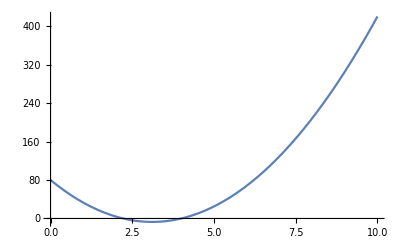

```mathematica
9 y^4-56 y^2 z+80 z^2/.z->α
Plot[80+9x^2-56x,{x,0,10}]
```

```mathematica
%//TeXForm
```

```mathematica
Sqrt[56^2-4*9*80]
```

16

```mathematica
Solve[9 y^4-56 y^2 z+80 z^2==0,y]
```

{{y→-2 √z},{y→2 √z},{y→-2/3 √5 √z},{y→(2 √5 √z)/3}}

```mathematica
(56-16)/18
```

20/9

```mathematica
(2 √5 √z)/3//N
```

1.49071 √z

```mathematica
Solve[9 y^4-56 y^2 z+80 z^2==0,y]
```

{{y→-2 √z},{y→2 √z},{y→-2/3 √5 √z},{y→(2 √5 √z)/3}}

```mathematica
Solve[(2 x^4+(y^2-2 z) z+x^2 (-3 y^2+8 z))==0,x]
```

{{x→-1/2 √(3 y^2-8 z-√(9 y^4-56 y^2 z+80 z^2))},{x→1/2 √(3 y^2-8 z-√(9 y^4-56 y^2 z+80 z^2))},{x→-1/2 √(3 y^2-8 z+√(9 y^4-56 y^2 z+80 z^2))},{x→1/2 √(3 y^2-8 z+√(9 y^4-56 y^2 z+80 z^2))}}

```mathematica
%/.z->y^2/4
```

0

```mathematica
%//FullSimplify
```

(y^2 (2 x^4+(y^2-2 z) z+x^2 (-3 y^2+8 z)))/(8 x (x^2-x y+z) (x (x+y)+z))

```mathematica
D[%,x]
```

(y^2 (8 x^3+2 x (-3 y^2+8 z)))/(8 x (x^2-x y+z) (x (x+y)+z))-(y^2 (2 x+y) (2 x^4+(y^2-2 z) z+x^2 (-3 y^2+8 z)))/(8 x (x^2-x y+z) (x (x+y)+z)^2)-((2 x-y) y^2 (2 x^4+(y^2-2 z) z+x^2 (-3 y^2+8 z)))/(8 x (x^2-x y+z)^2 (x (x+y)+z))-(y^2 (2 x^4+(y^2-2 z) z+x^2 (-3 y^2+8 z)))/(8 x^2 (x^2-x y+z) (x (x+y)+z))

```mathematica
Solve[%==0,x]
```

{{x→-(√(y^2-2 z))/(√2)},{x→(√(y^2-2 z))/(√2)},{x→-√z},{x→√z},{x→-(√(3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)},{x→(√(3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)},{x→-(√(3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)},{x→(√(3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)}}

```mathematica
((y^2 (2 x^4+(y^2-2 z) z+x^2 (-3 y^2+8 z)))/(8 x (x^2-x y+z) (x (x+y)+z))/.#)&@{{x->-(√(y^2-2 z))/(√2)},{x->(√(y^2-2 z))/(√2)},{x->-√z},{x->√z},{x->-(√(3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)},{x->(√(3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)},{x->-(√(3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)},{x->(√(3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)}}
```

{-(y^2 (1/2 (y^2-2 z)^2+(y^2-2 z) z+1/2 (y^2-2 z) (-3 y^2+8 z)))/(4 √2 √(y^2-2 z) (-((y-(√(y^2-2 z))/(√2)) √(y^2-2 z))/(√2)+z) ((y √(y^2-2 z))/(√2)+1/2 (y^2-2 z)+z)),(y^2 (1/2 (y^2-2 z)^2+(y^2-2 z) z+1/2 (y^2-2 z) (-3 y^2+8 z)))/(4 √2 √(y^2-2 z) (((y+(√(y^2-2 z))/(√2)) √(y^2-2 z))/(√2)+z) (-(y √(y^2-2 z))/(√2)+1/2 (y^2-2 z)+z)),-(y^2 ((y^2-2 z) z+2 z^2+z (-3 y^2+8 z)))/(8 √z (-(y-√z) √z+z) (y √z+2 z)),(y^2 ((y^2-2 z) z+2 z^2+z (-3 y^2+8 z)))/(8 √z ((y+√z) √z+z) (-y √z+2 z)),-(y^2 ((y^2-2 z) z+1/2 (-3 y^2+8 z) (3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2))+1/2 (3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2))^2))/(4 √2 √(3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2)) (z+(y √(3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)+1/2 (3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2))) (z-(√(3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2)) (y-(√(3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)))/(√2))),(y^2 ((y^2-2 z) z+1/2 (-3 y^2+8 z) (3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2))+1/2 (3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2))^2))/(4 √2 √(3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2)) (z-(y √(3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)+1/2 (3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2))) (z+(√(3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2)) (y+(√(3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)))/(√2))),-(y^2 ((y^2-2 z) z+1/2 (-3 y^2+8 z) (3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2))+1/2 (3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2))^2))/(4 √2 √(3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2)) (z+(y √(3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)+1/2 (3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2))) (z-(√(3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2)) (y-(√(3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)))/(√2))),(y^2 ((y^2-2 z) z+1/2 (-3 y^2+8 z) (3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2))+1/2 (3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2))^2))/(4 √2 √(3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2)) (z-(y √(3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)+1/2 (3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2))) (z+(√(3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2)) (y+(√(3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)))/(√2)))}

```mathematica
%//Simplify
```

{-(√(y^2-2 z))/(√2),(√(y^2-2 z))/(√2),-y^2/(4 √z),y^2/(4 √z),(y^2 (9 y^2-28 z-3 √(9 y^4-60 y^2 z+96 z^2)))/(8 (-3 y^2+10 z+√(9 y^4-60 y^2 z+96 z^2)) √(6 y^2-2 (10 z+√(9 y^4-60 y^2 z+96 z^2)))),(y^2 (-9 y^2+28 z+3 √(9 y^4-60 y^2 z+96 z^2)))/(8 (-3 y^2+10 z+√(9 y^4-60 y^2 z+96 z^2)) √(6 y^2-2 (10 z+√(9 y^4-60 y^2 z+96 z^2)))),-(y^2 (9 y^2-28 z+3 √(9 y^4-60 y^2 z+96 z^2)))/(8 √2 (3 y^2-10 z+√(9 y^4-60 y^2 z+96 z^2))^(3/2)),(y^2 (9 y^2-28 z+3 √(9 y^4-60 y^2 z+96 z^2)))/(8 √2 (3 y^2-10 z+√(9 y^4-60 y^2 z+96 z^2))^(3/2))}

```mathematica
{{x->-(√(y^2-2 z))/(√2)},{x->(√(y^2-2 z))/(√2)},{x->-√z},{x->√z},{x->-(√(3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)},{x->(√(3 y^2-10 z-√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)},{x->-(√(3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)},{x->(√(3 y^2-10 z+√3 √(3 y^4-20 y^2 z+32 z^2)))/(√2)}}//Simplify
```

{{x→-(√(y^2-2 z))/(√2)},{x→(√(y^2-2 z))/(√2)},{x→-√z},{x→√z},{x→-(√(3 y^2-10 z-√(9 y^4-60 y^2 z+96 z^2)))/(√2)},{x→√((3 y^2)/2-5 z-1/2 √(9 y^4-60 y^2 z+96 z^2))},{x→-(√(3 y^2-10 z+√(9 y^4-60 y^2 z+96 z^2)))/(√2)},{x→(√(3 y^2-10 z+√(9 y^4-60 y^2 z+96 z^2)))/(√2)}}